## Выполнил студент группы Э-1914 Кудряшов Георгий Вариант 22

### Метод Дихотомии

```mathematica
ClearAll[f,ϵ,x,a,b,δ,ϵk,i];
Subscript[A, 3]=0;
Subscript[A, 2]=7;
Subscript[A, 1]=2;
Subscript[A, 0]=1;
a=-3;
b=2;
ϵ=0.0001;
δ=ϵ/10;
f[x_]:=x^4+Subscript[A, 3]*x^3+Subscript[A, 2]*x^2+Subscript[A, 1]*x+Subscript[A, 0]
ϵk[a_,b_]:=(b-a)/2;
i=0;
While[ϵk[a,b]>=ϵ,Subscript[x, 1]=(a+b-δ)/2;Subscript[x, 2]=(a+b+δ)/2;
If[f[Subscript[x, 1]]<=f[Subscript[x, 2]],b=Subscript[x, 2],a=Subscript[x, 1]];i++;
Print@Column[{{"Номер итерации:",i},{"Границы:",{a,b}},{"x_1:",Subscript[x, 1]," x_2:",Subscript[x, 2]},{" x^*:",(b+a)/2," f(x^*):",f[(b+a)/2]}},Background->{Cyan,LightCyan}]]
```

{Номер итерации:,1}
{Границы:,{-0.500005,2}}
{x_1:,-0.500005, x_2:,-0.499995}
{ x^*:,0.749998, f(x^*):,6.75387}

{Номер итерации:,2}
{Границы:,{-0.500005,0.750003}}
{x_1:,0.749993, x_2:,0.750003}
{ x^*:,0.124999, f(x^*):,1.35961}

{Номер итерации:,3}
{Границы:,{-0.500005,0.125004}}
{x_1:,0.124994, x_2:,0.125004}
{ x^*:,-0.187501, f(x^*):,0.87233}

{Номер итерации:,4}
{Границы:,{-0.187506,0.125004}}
{x_1:,-0.187506, x_2:,-0.187496}
{ x^*:,-0.0312509, f(x^*):,0.944335}

{Номер итерации:,5}
{Границы:,{-0.187506,-0.0312459}}
{x_1:,-0.0312559, x_2:,-0.0312459}
{ x^*:,-0.109376, f(x^*):,0.865133}

{Номер итерации:,6}
{Границы:,{-0.187506,-0.109371}}
{x_1:,-0.109381, x_2:,-0.109371}
{ x^*:,-0.148438, f(x^*):,0.857846}

{Номер итерации:,7}
{Границы:,{-0.148443,-0.109371}}
{x_1:,-0.148443, x_2:,-0.148433}
{ x^*:,-0.128907, f(x^*):,0.858781}

{Номер итерации:,8}
{Границы:,{-0.148443,-0.128902}}
{x_1:,-0.128912, x_2:,-0.128902}
{ x^*:,-0.138673, f(x^*):,0.857635}

{Номер итерации:,9}
{Границы:,{-0.148443,-0.138668}}
{x_1:,-0.138678, x_2:,-0.138668}
{ x^*:,-0.143555, f(x^*):,0.857571}

{Номер итерации:,10}
{Границы:,{-0.14356,-0.138668}}
{x_1:,-0.14356, x_2:,-0.14355}
{ x^*:,-0.141114, f(x^*):,0.857561}

{Номер итерации:,11}
{Границы:,{-0.14356,-0.141109}}
{x_1:,-0.141119, x_2:,-0.141109}
{ x^*:,-0.142335, f(x^*):,0.857555}

{Номер итерации:,12}
{Границы:,{-0.14234,-0.141109}}
{x_1:,-0.14234, x_2:,-0.14233}
{ x^*:,-0.141724, f(x^*):,0.857555}

{Номер итерации:,13}
{Границы:,{-0.14234,-0.141719}}
{x_1:,-0.141729, x_2:,-0.141719}
{ x^*:,-0.14203, f(x^*):,0.857555}

{Номер итерации:,14}
{Границы:,{-0.14234,-0.142025}}
{x_1:,-0.142035, x_2:,-0.142025}
{ x^*:,-0.142182, f(x^*):,0.857555}

{Номер итерации:,15}
{Границы:,{-0.142187,-0.142025}}
{x_1:,-0.142187, x_2:,-0.142177}
{ x^*:,-0.142106, f(x^*):,0.857555}

```mathematica
Print["Полученное оптимальное значение x^*:",(b+a)/2," f(x^*):",f[(b+a)/2], " количество итераций: ", i]
```

Полученное оптимальное значение x^*:-0.142106 f(x^*):0.857555 количество итераций: 15

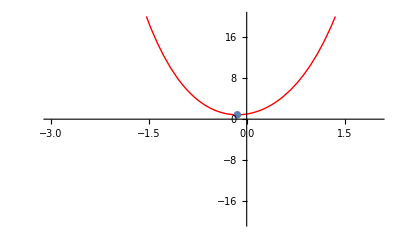

```mathematica
Show[{Plot[f[x],{x,-3,2},PlotRange->20,PlotStyle->{Thick,Red}],ListPlot[{{(b+a)/2,f[(b+a)/2]}}]}]
```

### Метод золотого сечения

{Номер итерации:,1}
{Границы:,{-1.09017,2}}
{x_1:,0.0901699, x_2:,0.81966}
{f(x_1):,1.23732, f(x_2):,7.79359}
{ x^*:,0.454915, f(x^*):,3.40129}

{Номер итерации:,2}
{Границы:,{-1.09017,0.81966}}
{x_1:,-0.36068, x_2:,0.0901699}
{f(x_1):,1.20619, f(x_2):,1.23732}
{ x^*:,-0.135255, f(x^*):,0.857882}

{Номер итерации:,3}
{Границы:,{-1.09017,0.0901699}}
{x_1:,-0.63932, x_2:,-0.36068}
{f(x_1):,2.74953, f(x_2):,1.20619}
{ x^*:,-0.5, f(x^*):,1.8125}

{Номер итерации:,4}
{Границы:,{-0.63932,0.0901699}}
{x_1:,-0.36068, x_2:,-0.188471}
{f(x_1):,1.20619, f(x_2):,0.872969}
{ x^*:,-0.274575, f(x^*):,0.984274}

{Номер итерации:,5}
{Границы:,{-0.36068,0.0901699}}
{x_1:,-0.188471, x_2:,-0.0820393}
{f(x_1):,0.872969, f(x_2):,0.88308}
{ x^*:,-0.135255, f(x^*):,0.857882}

{Номер итерации:,6}
{Границы:,{-0.36068,-0.0820393}}
{x_1:,-0.254249, x_2:,-0.188471}
{f(x_1):,0.948178, f(x_2):,0.872969}
{ x^*:,-0.22136, f(x^*):,0.902682}

{Номер итерации:,7}
{Границы:,{-0.254249,-0.0820393}}
{x_1:,-0.188471, x_2:,-0.147817}
{f(x_1):,0.872969, f(x_2):,0.857793}
{ x^*:,-0.168144, f(x^*):,0.862418}

{Номер итерации:,8}
{Границы:,{-0.188471,-0.0820393}}
{x_1:,-0.147817, x_2:,-0.122692}
{f(x_1):,0.857793, f(x_2):,0.860216}
{ x^*:,-0.135255, f(x^*):,0.857882}

{Номер итерации:,9}
{Границы:,{-0.188471,-0.122692}}
{x_1:,-0.163346, x_2:,-0.147817}
{f(x_1):,0.860793, f(x_2):,0.857793}
{ x^*:,-0.155581, f(x^*):,0.858862}

{Номер итерации:,10}
{Границы:,{-0.163346,-0.122692}}
{x_1:,-0.147817, x_2:,-0.138221}
{f(x_1):,0.857793, f(x_2):,0.857658}
{ x^*:,-0.143019, f(x^*):,0.857561}

{Номер итерации:,11}
{Границы:,{-0.147817,-0.122692}}
{x_1:,-0.138221, x_2:,-0.132289}
{f(x_1):,0.857658, f(x_2):,0.858231}
{ x^*:,-0.135255, f(x^*):,0.857882}

{Номер итерации:,12}
{Границы:,{-0.147817,-0.132289}}
{x_1:,-0.141886, x_2:,-0.138221}
{f(x_1):,0.857555, f(x_2):,0.857658}
{ x^*:,-0.140053, f(x^*):,0.857583}

{Номер итерации:,13}
{Границы:,{-0.147817,-0.138221}}
{x_1:,-0.144152, x_2:,-0.141886}
{f(x_1):,0.857586, f(x_2):,0.857555}
{ x^*:,-0.143019, f(x^*):,0.857561}

{Номер итерации:,14}
{Границы:,{-0.144152,-0.138221}}
{x_1:,-0.141886, x_2:,-0.140486}
{f(x_1):,0.857555, f(x_2):,0.857572}
{ x^*:,-0.141186, f(x^*):,0.85756}

{Номер итерации:,15}
{Границы:,{-0.144152,-0.140486}}
{x_1:,-0.142752, x_2:,-0.141886}
{f(x_1):,0.857558, f(x_2):,0.857555}
{ x^*:,-0.142319, f(x^*):,0.857555}

{Номер итерации:,16}
{Границы:,{-0.142752,-0.140486}}
{x_1:,-0.141886, x_2:,-0.141351}
{f(x_1):,0.857555, f(x_2):,0.857558}
{ x^*:,-0.141619, f(x^*):,0.857556}

{Номер итерации:,17}
{Границы:,{-0.142752,-0.141351}}
{x_1:,-0.142217, x_2:,-0.141886}
{f(x_1):,0.857555, f(x_2):,0.857555}
{ x^*:,-0.142051, f(x^*):,0.857555}

{Номер итерации:,18}
{Границы:,{-0.142217,-0.141351}}
{x_1:,-0.141886, x_2:,-0.141682}
{f(x_1):,0.857555, f(x_2):,0.857555}
{ x^*:,-0.141784, f(x^*):,0.857555}

{Номер итерации:,19}
{Границы:,{-0.142217,-0.141682}}
{x_1:,-0.142012, x_2:,-0.141886}
{f(x_1):,0.857555, f(x_2):,0.857555}
{ x^*:,-0.141949, f(x^*):,0.857555}

{Номер итерации:,20}
{Границы:,{-0.142217,-0.141886}}
{x_1:,-0.14209, x_2:,-0.142012}
{f(x_1):,0.857555, f(x_2):,0.857555}
{ x^*:,-0.142051, f(x^*):,0.857555}

{Номер итерации:,21}
{Границы:,{-0.14209,-0.141886}}
{x_1:,-0.142012, x_2:,-0.141964}
{f(x_1):,0.857555, f(x_2):,0.857555}
{ x^*:,-0.141988, f(x^*):,0.857555}

{Номер итерации:,22}
{Границы:,{-0.14209,-0.141964}}
{x_1:,-0.142042, x_2:,-0.142012}
{f(x_1):,0.857555, f(x_2):,0.857555}
{ x^*:,-0.142027, f(x^*):,0.857555}

{Номер итерации:,23}
{Границы:,{-0.14209,-0.142012}}
{x_1:,-0.142061, x_2:,-0.142042}
{f(x_1):,0.857555, f(x_2):,0.857555}
{ x^*:,-0.142051, f(x^*):,0.857555}

Полученное оптимальное значение x^*:-0.142051 f(x^*):0.857555 количество итераций: 23

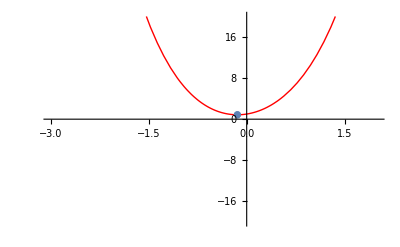

```mathematica
ClearAll[f,ϵ,x,a,b,δ,ϵk,i];
a=-3;
b=2;
ϵ=0.0001;
Subscript[x, 1]=N[a+(3-√5)/2(b-a)];
Subscript[x, 2]=a+b-Subscript[x, 1];
f[x_]:=x^4+Subscript[A, 3]*x^3+Subscript[A, 2]*x^2+Subscript[A, 1]*x+Subscript[A, 0];
l=b-a;
i=0;
While[l>ϵ,
If[f[Subscript[x, 1]]<=f[Subscript[x, 2]],b=Subscript[x, 2];Subscript[x, 2]=Subscript[x, 1];Subscript[x, 1]=a+b-Subscript[x, 1],
a=Subscript[x, 1];Subscript[x, 1]=Subscript[x, 2];Subscript[x, 2]=a+b-Subscript[x, 2]];
l=b-a;
i++;
Print@Column[{{"Номер итерации:",i},{"Границы:",{a,b}},{"x_1:",Subscript[x, 1]," x_2:",Subscript[x, 2]},{"f(x_1):",f[Subscript[x, 1]]," f(x_2):",f[Subscript[x, 2]]},{" x^*:",(b+a)/2," f(x^*):",f[(b+a)/2]}},Background->{Cyan,LightCyan}]]
Print["Полученное оптимальное значение x^*:",(b+a)/2," f(x^*):",f[(b+a)/2], " количество итераций: ", i]
Show[{Plot[f[x],{x,-3,2},PlotRange->20,PlotStyle->{Thick,Red}],ListPlot[{{(b+a)/2,f[(b+a)/2]}}]}]
```

### Решение задачи оптимизации, используя встроенные средства оптимизации Wolfram Mathematica

```mathematica
ClearAll[x];
Subscript[A, 3]=0;
Subscript[A, 2]=7;
Subscript[A, 1]=2;
Subscript[A, 0]=1;
Minimize[x^4+Subscript[A, 3]*x^3+Subscript[A, 2]*x^2+Subscript[A, 1]*x+Subscript[A, 0],x,Reals]
```

{1+2 Root-0.142Root[1+7 #1+2 #1^3&,1]-0.14203839676423557+7 (Root-0.142Root[1+7 #1+2 #1^3&,1]-0.14203839676423557)^2+(Root-0.142Root[1+7 #1+2 #1^3&,1]-0.14203839676423557)^4,{x→Root-0.142Root[1+7 #1+2 #1^3&,1]-0.14203839676423557}}